#### Inputs

```mathematica
targetS=-3+4x+2x^2-x^3;
targetS=x^2;
range={-3, 4, 0.01};
```

#### Starting

```mathematica
nestS[symb_,var_:x]:=Expand[symb/.var->symb]
funcS[symb_, var_:x]:=Function[dontusethisvariable, symb/.var->dontusethisvariable]
```

```mathematica
target=funcS[targetS];
```

```mathematica
fixedPoints=Sort[If[Im[#]==0,#,Nothing]&/@(Values[#][[1]]&/@NSolve[{x==targetS, x>=range[[1]], x<=range[[2]]}, x]), Less]
middleFixedPoint=fixedPoints[[Round[Length[fixedPoints]/2]]];
```

{0,1.}

```mathematica
(* First two terms of Maclaurin series to make a linear approximation around x = middleFixedPoint *)
macLaurinApproxTerms={target[middleFixedPoint],funcS[D[targetS,x]][middleFixedPoint]};

(* y = term[[1]]+term[[2]](x - fixedPoint) -> y = (term[[1]] - term[[2]]fixedPoint) + term[[2]]x *)
macLaurinSlopeInterceptApproxTerms={macLaurinApproxTerms[[1]] -macLaurinApproxTerms[[2]]*middleFixedPoint, macLaurinApproxTerms[[2]]};

linearRootApproxS=macLaurinSlopeInterceptApproxTerms[[1]]/(1+√macLaurinSlopeInterceptApproxTerms[[2]])+√macLaurinSlopeInterceptApproxTerms[[2]] x
linearRootApprox=funcS[linearRootApproxS];
```

0

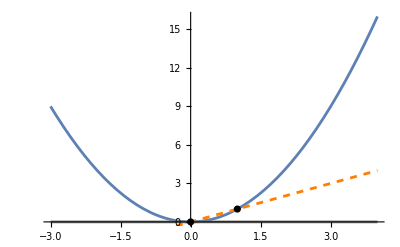

```mathematica
Show[
Plot[target[x], {x, range[[1]], range[[2]]}],
Plot[x, {x, range[[1]], range[[2]]}, PlotStyle->{Orange,Dashed}],
Plot[linearRootApprox[linearRootApprox[linearRootApprox[x]]], {x, range[[1]], range[[2]]}, PlotStyle->Gray],
ListPlot[Transpose[{fixedPoints, fixedPoints}], PlotStyle->Black]]
```

#### Approx Discussion

let f(x) be target(x) and fr(x) be the functional root of target(x).

at a fixed point, f^n(x) = x for all n. This means that
fr(x)=f(x)=x by definition.

In order to find an approximation at a different x, we need to know not only fr(x) but also fr(fr(x)). If fr(x) > x  (i.e., if the derivative at the fixed point is above 1), then we have to extrapolate out values of fr(fr(x))

f(x) = fr(fr(x)) by definition.
This means that we have to choose the value of fr(x) and fr of that value. This gives us an unconstrained solution.

given f and x, a valid solution can be made from fr(x) = w, fr(w) = f(x). w can be chosen freely.

w should be chosen to retain continuity

If w is chosen randomly...


f(x) = x^2

Lets have fr shift the input values by 0.05, then have those shifted values be mapped to the correct outputs:
fr(0) = 0, fr(fr(0)) = f(0) = 0
fr(0.1) = 0.15, fr(0.15) = 0.01
fr(0.2) = 0.25, fr(0.25) = 0.04
fr(0.3) = 0.35, fr(0.35) = 0.09

```mathematica
0.1^2
```

0.01

```mathematica
{0.15, 0.01, 0.25, 0.04, 0.35, 0.09, 0.45, 0.16, 0.55, 0.25, 0.65, 0.36, 0.75, 0.49, 0.85, 0.64, 0.95, 0.81, 1.05, 1.00}
```

{0.15,0.01,0.25,0.04,0.35,0.09,0.45,0.16,0.55,0.25,0.65,0.36,0.75,0.49,0.85,0.64,0.95,0.81,1.05,1.}

```mathematica
ListLinePlot[%36]
```

Out::intm: Machine-sized integer expected at position 1 in Out[False].

Out::intm: Machine-sized integer expected at position 1 in Out[36].

ListLinePlot::lpn: Out[36] is not a list of numbers or pairs of numbers.

ListLinePlot[%36]

On this plot, it turns every other point into being on the line y=x+0.05 and the remaining points into y=f(x)

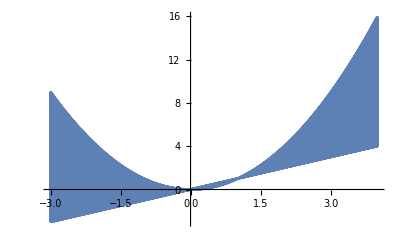

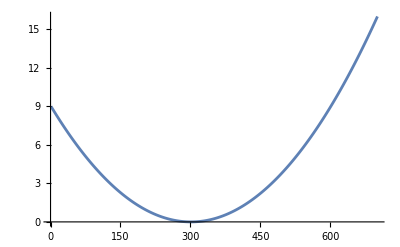

-Graphics-

```mathematica
rs2=range[[3]]/2;
approxPoints=Sort[Join[Table[{x, x+rs2}, {x, range[[1]], range[[2]], range[[3]]}], Table[{x+rs2, targetS}, {x, range[[1]], range[[2]], range[[3]]}]]];
approxFunc[x_]:=Interpolation[approxPoints,InterpolationOrder->1][x]
ListLinePlot[approxPoints]
ListLinePlot[approxFunc[approxFunc[#]]&/@(Range@@range)]
ListLinePlot[(targetS/.x->#)&/@(Range@@range)]
```

#### New Approximation Method

```mathematica
Show[
Plot[target[x], {x, range[[1]], range[[2]]}],
Plot[x, {x, range[[1]], range[[2]]}, PlotStyle->{Orange,Dashed}],
Plot[linearRootApprox[linearRootApprox[linearRootApprox[x]]], {x, range[[1]], range[[2]]}, PlotStyle->Gray],
ListPlot[Transpose[{fixedPoints, fixedPoints}], PlotStyle->Black]]
```

-Graphics-

```mathematica
xinit=N[(range[[2]]-range[[1]])/2 + range[[1]]]
w=1;
f[x_]:=target[x];
Min[Abs/@(xinit-fixedPoints)]
```

0.5

0.5

```mathematica
findFRL[xi_, wi_]:=Module[{xf=xi, wf=wi, frlf=<||>},
While[range[[1]]<=xf<=range[[2]]&&(Min[Abs/@(xf-fixedPoints)]>=10^-10),
frlf[xf]=wf;
frlf[wf]=f[xf];
wf=f[xf];
xf=wf;]; 
frlf
]
(*findFRL[xinit, w]*)
```

```mathematica
N[Mean[Length[findFRL[RandomReal[],RandomReal[]]]&/@Range[0, 1000]]]
```

6.7962

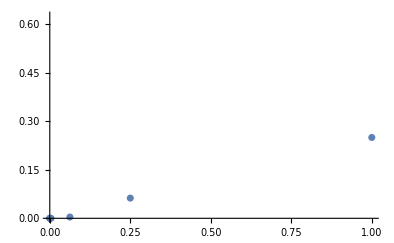

```mathematica
frl=findFRL[xinit, w];
ListPlot[Transpose[{Keys[frl], Values[frl]}]]
```

```mathematica
Plot3D[Length[findFRL[xit,wit]], {xit, 0, 1}, {wit, 0, 1}]
```

-Graphics3D-

```mathematica
maxLengthFRL=(Range@@range)[[#]]&/@(First[Position[#, Max[#]]]&@Table[Length[findFRL[xit, wit]], {xit, range[[1]], range[[2]], range[[3]]}, {wit, range[[1]], range[[2]], range[[3]]}])
```

{-0.99,-3.}

```mathematica
maxLengthFRLIndices=Position[#, Max[#]]&@Table[Length[findFRL[xit, wit]], {xit, range[[1]], range[[2]], range[[3]]}, {wit, range[[1]], range[[2]], range[[3]]}];
```

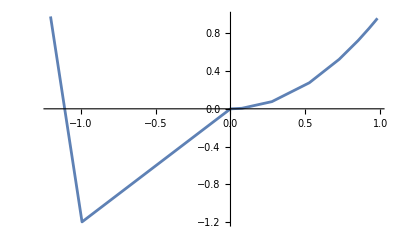
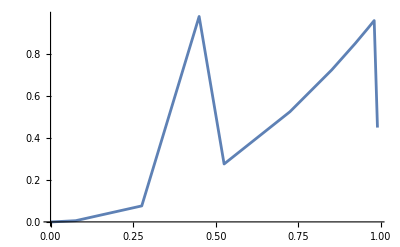
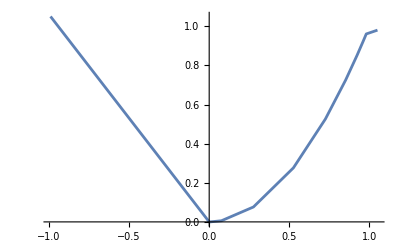
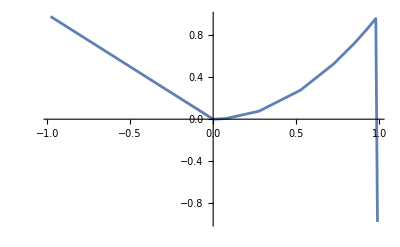
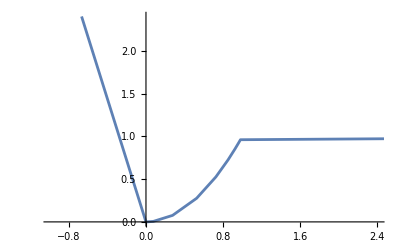
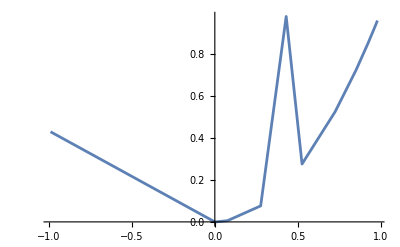
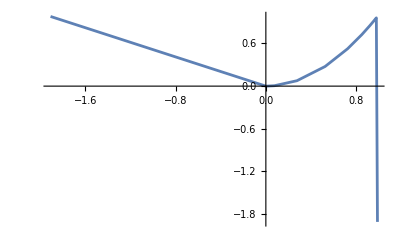
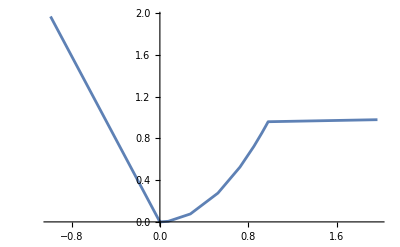

```mathematica
ListLinePlot[Sort@Transpose[{Keys[findFRL@@#], Values[findFRL@@#]}]]&/@({(Range@@range)[[#1]], (Range@@range)[[#2]]}&@@@RandomChoice[maxLengthFRLIndices, 20])
```

```mathematica
maxLengthFRL=(Range@@range)[[#]]&/@First[maxLengthFRLIndices]
frl=findFRL@@maxLengthFRL
```

{-0.99,-3.}

<|-0.99→-3.,-3.→0.9801,0.9801→0.960596,0.960596→0.922745,0.922745→0.851458,0.851458→0.72498,0.72498→0.525596,0.525596→0.276252,0.276252→0.076315,0.076315→0.00582398,0.00582398→0.0000339187,0.0000339187→1.15048×10^-9,1.15048×10^-9→1.3236×10^-18|>

{{-3.,0.9801},{-0.99,-3.},{1.15048×10^-9,1.3236×10^-18},{0.0000339187,1.15048×10^-9},{0.00582398,0.0000339187},{0.076315,0.00582398},{0.276252,0.076315},{0.525596,0.276252},{0.72498,0.525596},{0.851458,0.72498},{0.922745,0.851458},{0.960596,0.922745},{0.9801,0.960596}}

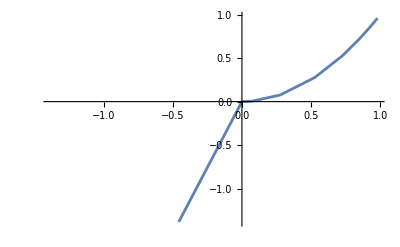

InterpolatingFunction::dmval: Input value {0.99} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.999216} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

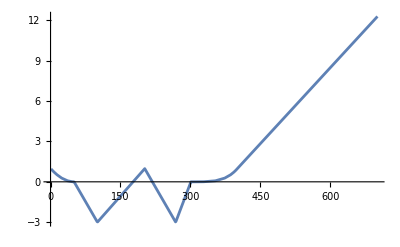

-Graphics-

InterpolatingFunction::dmval: Input value {0.99} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.999216} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

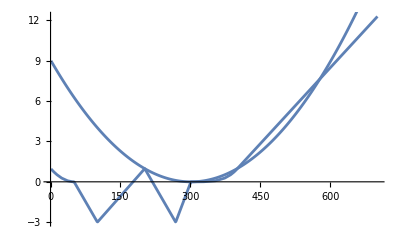

```mathematica
approxPoints=Sort@Transpose[{Keys[frl], Values[frl]}]
approxFunc[x_]:=Interpolation[approxPoints,InterpolationOrder->1][x]
ListLinePlot[approxPoints]
ListLinePlot[approxFunc[approxFunc[#]]&/@(Range@@range)]
ListLinePlot[(targetS/.x->#)&/@(Range@@range)]
Show[ListLinePlot[approxFunc[approxFunc[#]]&/@(Range@@range)],
ListLinePlot[(targetS/.x->#)&/@(Range@@range)]]
```